```mathematica
ρ=(a+b)/2;
```

```mathematica
Solve[ A0*(ρ^0-b^1*ρ^-1)+A1*LegendreP[2,Cos[0]]*(-b^5*ρ^-3+ρ^2)==12&& A0*(ρ^0-b^1*ρ^-1)+A1*LegendreP[2,Cos[π/4]]*(-b^5*ρ^-3+ρ^2)==6,{A0,A1}]
```

{{A0→-12,A1→-864/781}}

2592/781 (-32/ρ^3+ρ^2) Cos[ϕ] Sin[ϕ]

36156/781

6

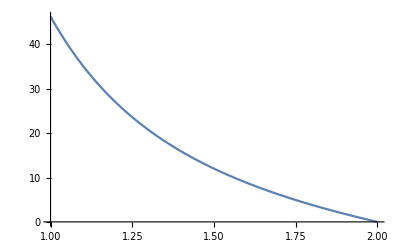

-Graphics3D-

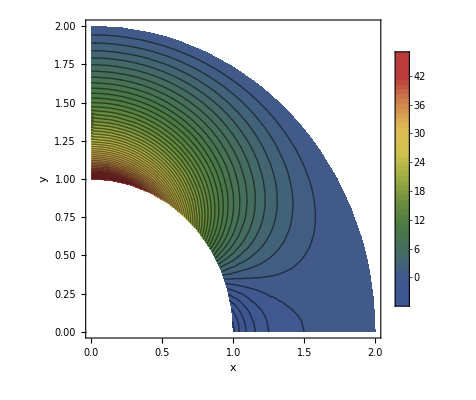

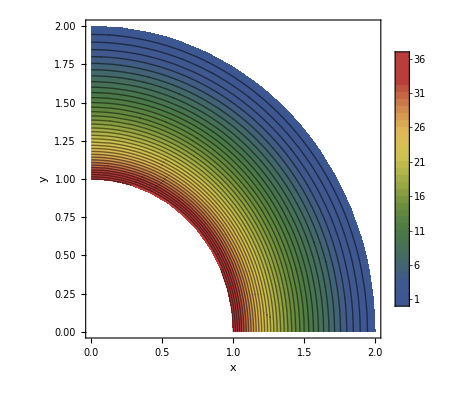

```mathematica
u[ρ_,ϕ_]:=-12*(ρ^0-b^1*ρ^-1)-864/781*LegendreP[2,Cos[ϕ]]*(-b^5*ρ^-3+ρ^2)
f[ρ_,ϕ_]:=-36*(ρ^0-b^1*ρ^-1)
D[u[ρ,ϕ],ϕ]
u[1,0]
u[(a+b)/2,π/4]
Plot[u[ρ,0],{ρ,1,2}]
Plot3D[u[ρ,ϕ],{ρ,a,b},{ϕ,0,π/2}]
ContourPlot[u[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{1,2},{0,π/2}],BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,560,1],PlotRange->All,PlotLegends->Automatic]
ContourPlot[f[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{1,2},{0,π/2}],BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,100,1],PlotLegends->Automatic]
```

```mathematica
Cos[π/4]
```

1/(√2)

```mathematica
Tfinal[ϕ_]:=20088/781*(Cos[ϕ])^2-2010/781
```

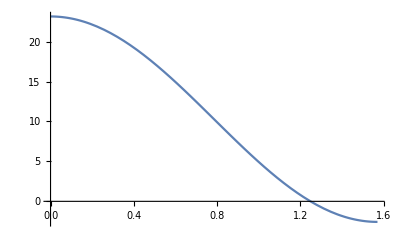

```mathematica
Plot[Tfinal[ϕ],{ϕ,0,π/2}]
```